### Константы

```mathematica
ME=10^10;ν=0.3;λ=(ν ME)/((1+ν)(1-2ν));μ=ME/(2(1+ν)); dz=-0.1;U0=1/100;
b=0.6;a=1; p0=P0=10000;
bx=1;by=1;
```

### [i,k] — Перемещения в направлении i, от нагрузки, равномерно распределённой в направлении k, по прямоугольной области(a на b) в виде скомпилированных функций

```mathematica
U[1,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 x3 (λ+μ))/(8 π μ (λ+2 μ))*(Log[x2+√(x1^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];
```

```mathematica
U[2,3] =  Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 x3 (λ+μ))/(8 π μ (λ+2 μ))*(Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];
```

```mathematica
U[3,3] =  Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];p0/(8 π μ (λ+2 μ))*(2 x3 μ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])+(λ+3 μ) (x2 (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)])+x1 (Log[x2+√(x1^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)])+(-b+x2) (-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])+(-a+x1) (-Log[x2+√((-a+x1)^2+x2^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])))
],
CompilationTarget->"C"
];
```

### [i,j,k] — Напряжения i,j от нагрузки равномерно распределённой в направлении k, по прямоугольной области (a на b) в виде скомпилированных функций

```mathematica
σ[1,1,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*(x3 (λ+μ) ((x1 x2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2))/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) (-b+x2))/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+λ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[1,2,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ))*(-1/(√(x1^2+x2^2+x3^2))+1/(√((-a+x1)^2+x2^2+x3^2))+1/(√(x1^2+(-b+x2)^2+x3^2))-1/(√((-a+x1)^2+(-b+x2)^2+x3^2)))
],
CompilationTarget->"C"
];
```

```mathematica
σ[1,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ)) ((λ+μ)*((x2 x3^2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))-(x2 x3^2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-((-b+x2) x3^2)/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-b+x2) x3^2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+μ (Log[x2+√(x1^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[2,2,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*(x3 (λ+μ) ((x1 x2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2))/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) (-b+x2))/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+λ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[2,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*((λ+μ) ((x1 x3^2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x3^2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 x3^2)/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) x3^2)/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+μ (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[3,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ)) (-(x1 x2 (x1^2+x2^2+2 x3^2))/((x1^2+x3^2) (x2^2+x3^2) √(x1^2+x2^2+x3^2))+((-a+x1) x2 ((-a+x1)^2+x2^2+2 x3^2))/(((-a+x1)^2+x3^2) (x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))+(x1 (-b+x2) (x1^2+(-b+x2)^2+2 x3^2))/((x1^2+x3^2) ((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((a-x1) (-b+x2) ((-a+x1)^2+(-b+x2)^2+2 x3^2))/(((-a+x1)^2+x3^2) ((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+p0/(4 π) (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])

],
CompilationTarget->"C"
];
```

```mathematica
σ1[x1_,x2_,x3_,a_,b_] =
(p0 x3 (λ+μ))/(4 π (λ+2 μ)) (-(x1 x2 (x1^2+x2^2+2 x3^2))/((x1^2+x3^2) (x2^2+x3^2) √(x1^2+x2^2+x3^2))+((-a+x1) x2 ((-a+x1)^2+x2^2+2 x3^2))/(((-a+x1)^2+x3^2) (x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))+(x1 (-b+x2) (x1^2+(-b+x2)^2+2 x3^2))/((x1^2+x3^2) ((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((a-x1) (-b+x2) ((-a+x1)^2+(-b+x2)^2+2 x3^2))/(((-a+x1)^2+x3^2) ((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+p0/(4 π) (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]);
```

## 1) Графики

### Графики напряжений

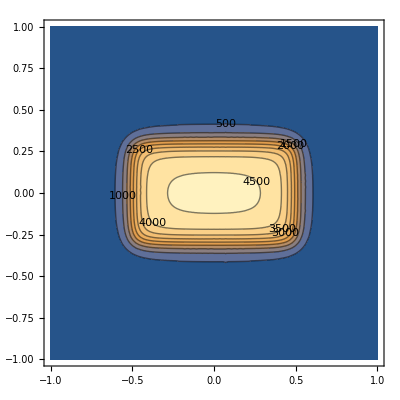

```mathematica
Print[ContourPlot[σ[3,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

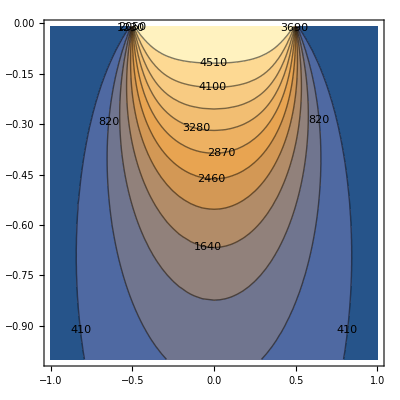

```mathematica
Print[ContourPlot[σ[3,3,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

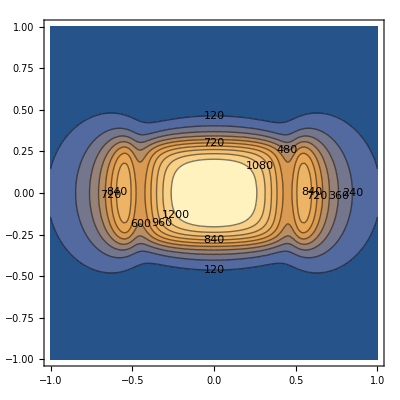

```mathematica
Print[ContourPlot[σ[1,1,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

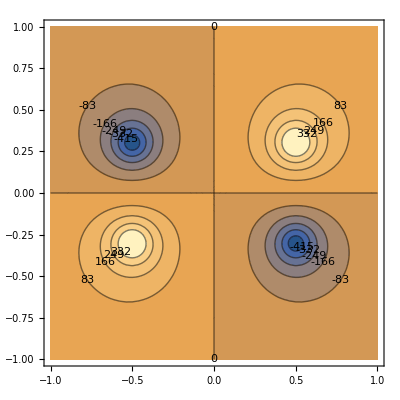

```mathematica
Print[ContourPlot[σ[1,2,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

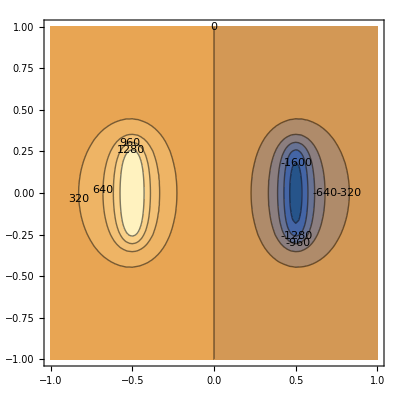

```mathematica
Print[ContourPlot[σ[1,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

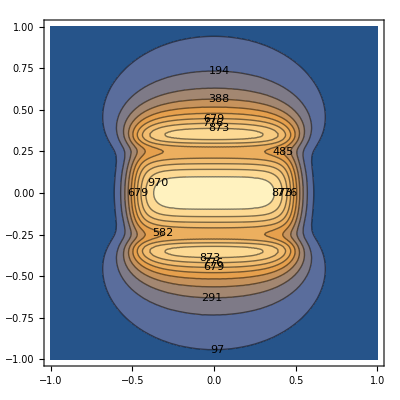

```mathematica
Print[ContourPlot[σ[2,2,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

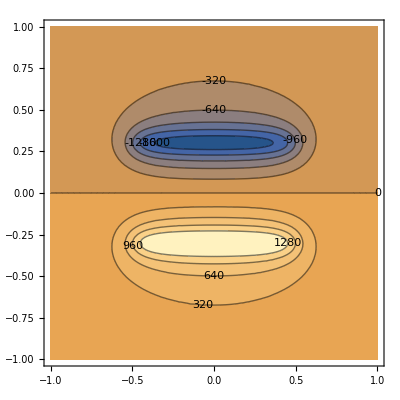

```mathematica
Print[ContourPlot[σ[2,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

### Графики перемещений

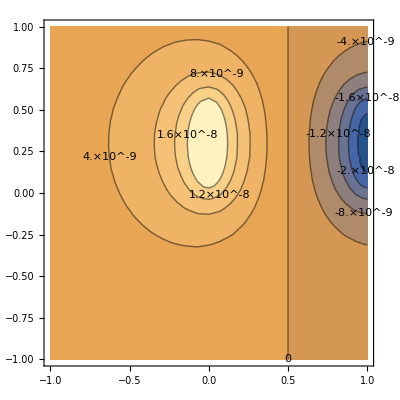

```mathematica
Print[ContourPlot[U[1,3][x,a,y,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

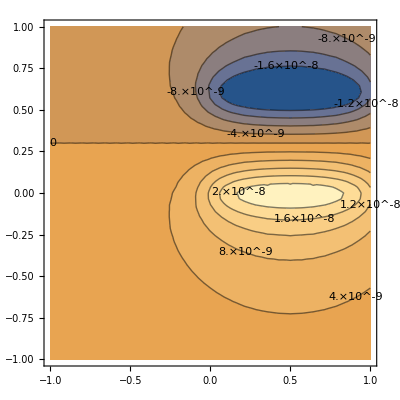

```mathematica
Print[ContourPlot[U[2,3][x,a,y,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

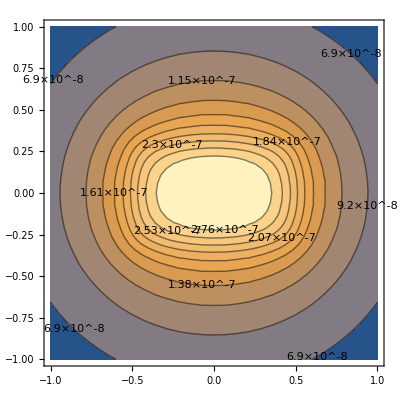

```mathematica
Print[ContourPlot[U[3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

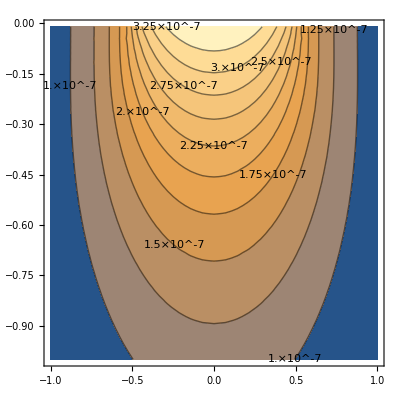

```mathematica
Print[ContourPlot[U[3,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

## 2) Граничная задача для вдавливания плоского эллиптического штампа

#### Инициализация и графики поверхностного распределения и дискретизации функции поверхностного распределения

```mathematica
Pressure[x_,y_,a_,b_,p0_]=If[(x/a)^2+(y/b)^2≤1,Re[P0 √(1-(x/a)^2-(y/b)^2)],0];
Displacement[x_,y_,a_,b_,p0_]=If[(x/a)^2+(y/b)^2≤1,U0,0];
(*Pressure[x_,y_,a_,b_,p0_]=If[(x/a)^2+(y/b)^2≤1,P0,0];*)
s=1.5*a;(*размер расчетной области*)
(*Установить h = 3a/19 для n = 20*)
h= 3a /39;(*размер ГЭ*)
n=2 s/h+1(*number of elementary units*)
(*array of X-coordinates*)
X=Table[xh,{xh,-s,s,h}];
Y=Table[yh,{yh,-s,s,h}];
Plot3D[Pressure[x,y,a,b,P0],{x,-s,s},{y,-s,s},AxesLabel->Automatic,PlotRange->All]
```

40.

-Graphics3D-

```mathematica
DisplacementTab=Table[Displacement[X[[xi]],Y[[yj]],a,b,P0]//N,{xi,1,n},{yj,1,n}];
PressureTab=Table[Pressure[X[[xi]],Y[[yj]],a,b,P0]//N,{xi,1,n},{yj,1,n}];
ListPlot3D[DisplacementTab,InterpolationOrder->0,Filling->None,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
BoundaryElements=Table[{X[[xi]],Y[[yj]],DisplacementTab[[xi,yj]]},{xi,1,n},{yj,1,n}];
```

### Получение решения последовательно

```mathematica
Pk1 = Table[Subscript[p, k],{k,1,n^2}];
(*PotV[xj_,yj_] =Sum[σ1[X[[m]]-xj,Y[[o]]-yj,-0.001,h,h]*Pk1[[n m +o-n]],{m,1,n},{o,1,n}];
FPT=Flatten[PressureTab];*)
```

```mathematica
(*Equationq=Flatten[Table[PotV[X[[i]],Y[[j]]]==PressureTab[[i,j]],{i,1,n},{j,1,n}]];*)
Equationq=Flatten[Table[Sum[U[3,3][X[[m]]-X[[i]],h,Y[[o]]-Y[[j]],h,0.01,p0,λ,μ]*Pk1[[n m +o-n]],{m,1,n},{o,1,n}]==DisplacementTab[[i,j]],{i,1,n},{j,1,n}]];
```

```mathematica
Solq = Solve[Equationq,Pk1];
SolNq=Table[Solq[[1,i,2]],{i,1,n*n}];
SolN1q = Table[SolNq[[n  i +j-n]],{i,1,n},{j,1,n}];
ListPlot3D[SolN1q,InterpolationOrder->0,Filling->Automatic,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
DIntSRes=Function[{x,y,z},∑_(i=1)^n ∑_(j=1)^n U[3,3][X[[i]]-x,h,Y[[j]]-y,h,z,p0,λ,μ]*SolN1q[[i,j]]];
```

```mathematica
Resq=Table[DIntSRes[X[[i]],Y[[j]],0.01],{i,1,n},{j,1,n}];
```

```mathematica
ListPlot3D[Resq,InterpolationOrder->0,Filling->None,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
(*CUDAQ[] *)
```

```mathematica
(*CUDAResourcesInstall[]*)
```

```mathematica
(*Table[U[3,3][X[[i]]-X[[1]],h,Y[[i]]-Y[[1]],h,0.01,p0,λ,μ],{i,1,n},{j,1,n}]//MatrixForm*)
```

решение для σ:

```mathematica
Equationq=Flatten[Table[Sum[σ[3,3,3][X[[m]]-X[[i]],h,Y[[o]]-Y[[j]],h,0.01,p0,λ,μ]*Pk1[[n m +o-n]],{m,1,n},{o,1,n}]==-PressureTab[[i,j]],{i,1,n},{j,1,n}]];

Solq = Solve[Equationq,Pk1];
SolNq=Table[Solq[[1,i,2]],{i,1,n*n}];
SolN1q = Table[SolNq[[n  i +j-n]],{i,1,n},{j,1,n}];
ListPlot3D[SolN1q,InterpolationOrder->0,Filling->Automatic,Mesh->None,PlotRange->All]
```

-Graphics3D-